```mathematica
Clear[kzVector,Plot1,bb]
```

```mathematica
kzVector = N@Subdivide[-π,π,200]
```

{-3.14159,-3.11018,-3.07876,-3.04734,-3.01593,-2.98451,-2.9531,-2.92168,-2.89027,-2.85885,-2.82743,-2.79602,-2.7646,-2.73319,-2.70177,-2.67035,-2.63894,-2.60752,-2.57611,-2.54469,-2.51327,-2.48186,-2.45044,-2.41903,-2.38761,-2.35619,-2.32478,-2.29336,-2.26195,-2.23053,-2.19911,-2.1677,-2.13628,-2.10487,-2.07345,-2.04204,-2.01062,-1.9792,-1.94779,-1.91637,-1.88496,-1.85354,-1.82212,-1.79071,-1.75929,-1.72788,-1.69646,-1.66504,-1.63363,-1.60221,-1.5708,-1.53938,-1.50796,-1.47655,-1.44513,-1.41372,-1.3823,-1.35088,-1.31947,-1.28805,-1.25664,-1.22522,-1.19381,-1.16239,-1.13097,-1.09956,-1.06814,-1.03673,-1.00531,-0.973894,-0.942478,-0.911062,-0.879646,-0.84823,-0.816814,-0.785398,-0.753982,-0.722566,-0.69115,-0.659734,-0.628319,-0.596903,-0.565487,-0.534071,-0.502655,-0.471239,-0.439823,-0.408407,-0.376991,-0.345575,-0.314159,-0.282743,-0.251327,-0.219911,-0.188496,-0.15708,-0.125664,-0.0942478,-0.0628319,-0.0314159,0.,0.0314159,0.0628319,0.0942478,0.125664,0.15708,0.188496,0.219911,0.251327,0.282743,0.314159,0.345575,0.376991,0.408407,0.439823,0.471239,0.502655,0.534071,0.565487,0.596903,0.628319,0.659734,0.69115,0.722566,0.753982,0.785398,0.816814,0.84823,0.879646,0.911062,0.942478,0.973894,1.00531,1.03673,1.06814,1.09956,1.13097,1.16239,1.19381,1.22522,1.25664,1.28805,1.31947,1.35088,1.3823,1.41372,1.44513,1.47655,1.50796,1.53938,1.5708,1.60221,1.63363,1.66504,1.69646,1.72788,1.75929,1.79071,1.82212,1.85354,1.88496,1.91637,1.94779,1.9792,2.01062,2.04204,2.07345,2.10487,2.13628,2.1677,2.19911,2.23053,2.26195,2.29336,2.32478,2.35619,2.38761,2.41903,2.45044,2.48186,2.51327,2.54469,2.57611,2.60752,2.63894,2.67035,2.70177,2.73319,2.7646,2.79602,2.82743,2.85885,2.89027,2.92168,2.9531,2.98451,3.01593,3.04734,3.07876,3.11018,3.14159}

```mathematica
NumPoints=Dimensions[kzVector][[1]]
```

201

```mathematica
bb = Import["/home/archisman/Documents/GitHub/quasicrystals/plots/plots for paper/temp/wsm plots m = 4/dataLandau_+8and+6Irrational_m=4_Parent32x32.dat"];
```

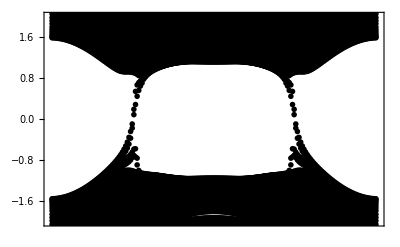

```mathematica
Plot1=Show[ListPlot[bb,PlotRange-> { {-3.14,3.14} ,{-2,2}},PlotStyle->{PointSize[0.01],Black}],BaseStyle-> 18,Frame-> True,FrameStyle-> {{Thick,Black},{Thick,Black},{Thick,Black},{Thick,Black}},Axes->{True,False},FrameTicks->{None,Automatic}]
```

```mathematica
Dimensions[bb]
```

{33034,2}

```mathematica
FactorInteger[Dimensions[bb][[1]]]
```

{{2,1},{83,1},{199,1}}

```mathematica
Dimensions[kzVector][[1]]
```

201

```mathematica
A = N[Dimensions[bb][[1]]/(2* (Dimensions[kzVector][[1]]-2))]
```

83.

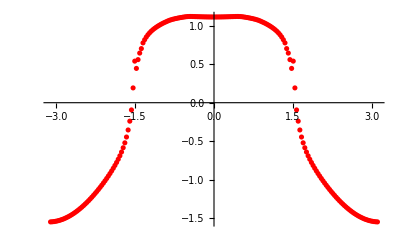

```mathematica
LandauLevelMixed1 = {};
Do[LandauLevelMixed1 = Append[LandauLevelMixed1,bb[[A + n *2*A]]],{n,0,Dimensions[kzVector][[1]]-3}];
Show[ListPlot[LandauLevelMixed1,PlotStyle->Red]]
```

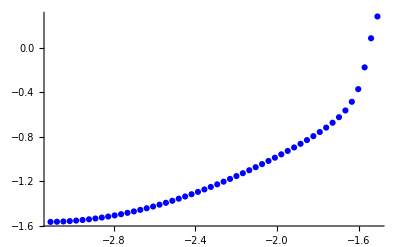

```mathematica
LandauLevelMixed21 = {};
Do[LandauLevelMixed21 = Append[LandauLevelMixed21,bb[[A -1+ n *2*A]]],{n,0,Floor[(Dimensions[kzVector][[1]]-3)*1/4+2]}];
Show[ListPlot[LandauLevelMixed21,PlotStyle->Blue,PlotRange->All]]
```

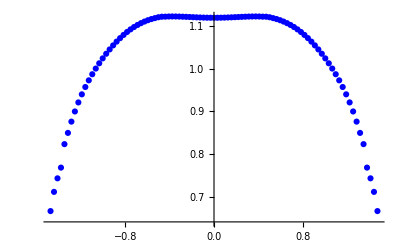

```mathematica
LandauLevelMixed22 = {};
Do[LandauLevelMixed22 = Append[LandauLevelMixed22,bb[[A +1+ n *2*A]]],{n,Ceiling[(Dimensions[kzVector][[1]]-3)*1/4+2],Floor[(Dimensions[kzVector][[1]]-3)*3/4-2]}];
Show[ListPlot[LandauLevelMixed22,PlotStyle->Blue,PlotRange->All]]
```

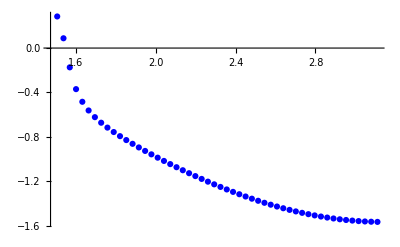

```mathematica
LandauLevelMixed23 = {};
Do[LandauLevelMixed23 = Append[LandauLevelMixed23,bb[[A -1+ n *2*A]]],{n,Ceiling[(Dimensions[kzVector][[1]]-3)*3/4-2],Dimensions[kzVector][[1]]-3}];
Show[ListPlot[LandauLevelMixed23,PlotStyle->Blue,PlotRange->All]]
```

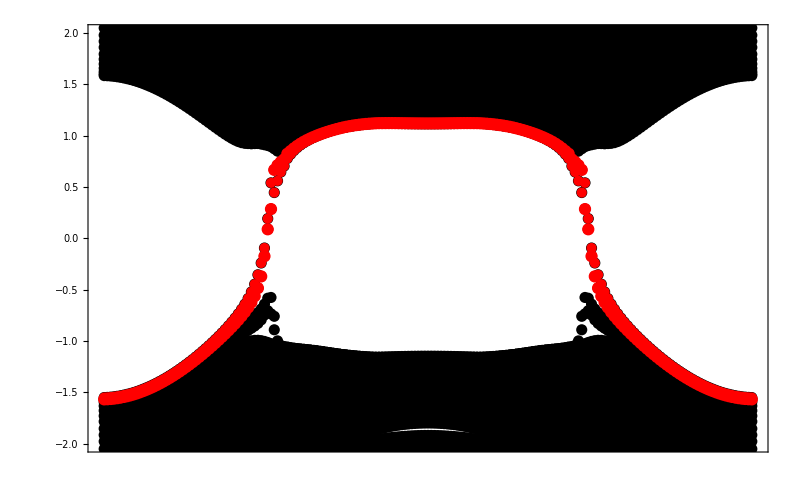

```mathematica
Show[Plot1,ListPlot[LandauLevelMixed1,PlotStyle->Red],ListPlot[LandauLevelMixed21,PlotStyle->Red],ListPlot[LandauLevelMixed22,PlotStyle->Red],ListPlot[LandauLevelMixed23,PlotStyle->Red],ImageSize-> 800,BaseStyle-> 36]
```